```mathematica
$UserBaseDirectory
Needs["MagneticTB`"]
spog=msgop[bnsdict[{123,342}]];
init[
lattice->{{a,0,0},{0,a,0},{0,0,c}},
lattpar->{a->1,c->10},
wyckoffposition->{{{0.5,0.0,0.5},{0,0,1}}},
symminformation->spog,
basisFunctions->{{"dz2up","dz2dn"}}
];
ham=Sum[symham[i],{i,3}];
MatrixForm[ham]
```

/Users/yxche/Library/Wolfram

Magnetic space group (BNS): {123.342,P4'/mm'm}

Lattice: TetragonalP

Primitive Lattice Vactor: {{a,0,0},{0,a,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{0,a,0},{0,0,c}}

Double Value Rep.

Generators:{{"2z",F},{"2-xy",F},{"-1",F},{"2x",T}}

params:{e1,e2}

params:{t1,t2}

params:{r1,r2,r3,r4}

(e1+ⅇ^(-ⅈ ky) r1+ⅇ^(ⅈ ky) r1+ⅇ^(-ⅈ kx) r3+ⅇ^(ⅈ kx) r3 | 0 | ⅇ^(ⅈ (-kx/2-ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (kx/2+ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (kx/2-ky/2)) (ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2+ky/2)) (ⅈ t1+t2) | 0
0 | e2+ⅇ^(-ⅈ ky) r2+ⅇ^(ⅈ ky) r2+ⅇ^(-ⅈ kx) r4+ⅇ^(ⅈ kx) r4 | 0 | ⅇ^(ⅈ (kx/2-ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2+ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2-ky/2)) (ⅈ t1+t2)+ⅇ^(ⅈ (kx/2+ky/2)) (ⅈ t1+t2)
ⅇ^(ⅈ (kx/2-ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2+ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2-ky/2)) (ⅈ t1+t2)+ⅇ^(ⅈ (kx/2+ky/2)) (ⅈ t1+t2) | 0 | e2+ⅇ^(-ⅈ kx) r2+ⅇ^(ⅈ kx) r2+ⅇ^(-ⅈ ky) r4+ⅇ^(ⅈ ky) r4 | 0
0 | ⅇ^(ⅈ (-kx/2-ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (kx/2+ky/2)) (-ⅈ t1+t2)+ⅇ^(ⅈ (kx/2-ky/2)) (ⅈ t1+t2)+ⅇ^(ⅈ (-kx/2+ky/2)) (ⅈ t1+t2) | 0 | e1+ⅇ^(-ⅈ kx) r1+ⅇ^(ⅈ kx) r1+ⅇ^(-ⅈ ky) r3+ⅇ^(ⅈ ky) r3)

```mathematica
path={
{{{0,0,0},{1/2,0,0}},{"G","X"}},
{{{1/2,0,0},{1/2,1/2,0}},{"X","M"}},
{{{1/2,1/2,0},{0,0,0}},{"M","G"}},
{{{0,0,0},{-1/2,1/2,0}},{"G","M'"}},
{{{-1/2,1/2,0},{0,1/2,0}},{"M'","X'"}},
{{{0,1/2,0},{0,0,0}},{"X'","G"}}
};
bandManipulate[path,20,ham]
```

Number of params:8

params:{e1,e2,r1,r2,r3,r4,t1,t2}

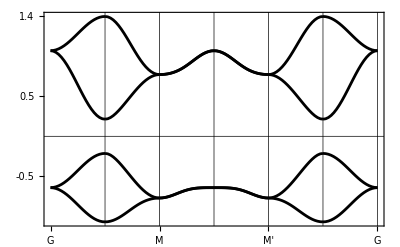

```mathematica
fig = bandplot[path, 20, ham, {e1->0.8,e2->-0.6,r1->0.2,r2->0.1,r3->-0.1,r4->-0.1,t1->0.1,t2->0.}]
```